### Perturbed Gene Evolution

Should run at scale with AWS to see what these guys look like, I bet they’ll look interesting

```mathematica
SeedRandom[4447];
als = Reap[
evo=NestList[Module[{}, 
ru={{"[◼]", "RandomRuleMutation"}}[First[#]];
ca = CellularAutomaton[ru, {{1}, 0}, 100];
lt = {{"[◼]", "TestCALifeTime"}}[ca];
rus =Table[{{"[◼]", "RandomRuleMutation"}}[ru], Floor[If[# == -Infinity, 0, #]&[Min[Last[#]]] / 10]];
cas= CellularAutomaton[#, {{1}, 0}, 100]&/@ rus;
lts=Prepend[{{"[◼]", "TestCALifeTime"}}/@ cas, lt];
Sow[lts];
If[Min[lts]>=Min[Last[#]],{ru,lts},#]
]&,{{0,4,1},{0, 0}},500]][[2, 1]];
```

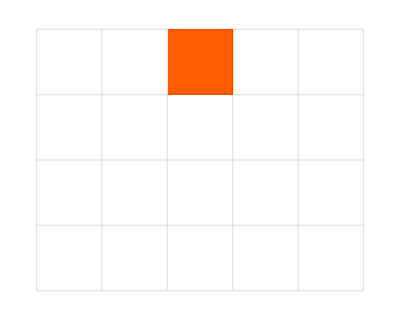
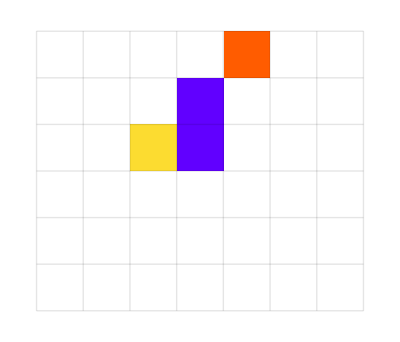
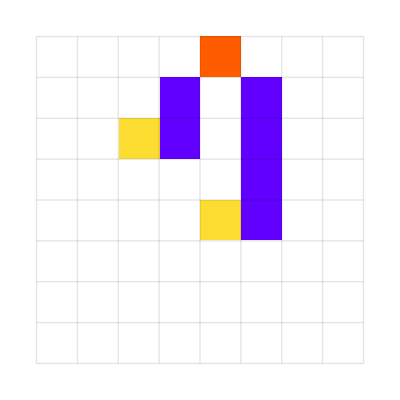
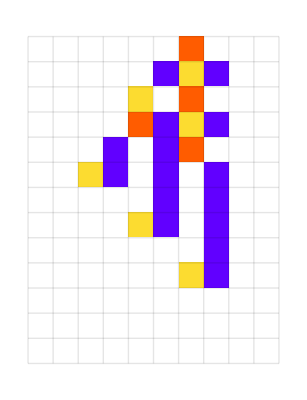
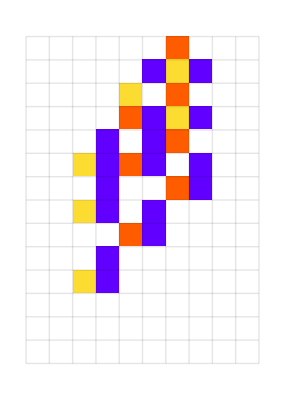
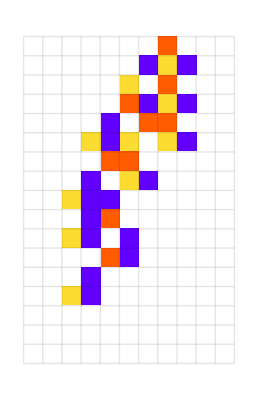
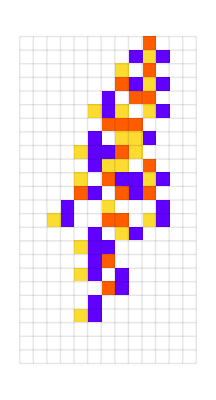
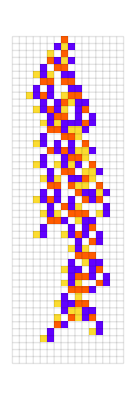
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
e2=Rest[First/@SplitBy[evo,Last]];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},#[[-1, 1]]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
e2]
```

### Changing fitness function

```mathematica
gens=Keys[{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]];
```

```mathematica
gensCallouts={{"[◼]", "quickDepict"}}[{2,2},#,{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"][#]]&/@gens;
```

```mathematica
{gensRuleMap,ruleGensMap}={{"[◼]", "MarkovRuleMap"}}[First/@PositionIndex[gens]];
```

```mathematica
size=Length[ruleGensMap];
```

```mathematica
ruleIndex=AssociationThread[Keys[ruleGensMap],Range[size]];
```

```mathematica
gensRuleIndices=Lookup[gensRuleMap,Key@#]&/@gens;
```

(Long computation time + 8 GB)

```mathematica
arMarkovWeights=Parallelize@AssociationMap[{{"[◼]", "FitnessMarkovWeights"}}[{{"[◼]", "arFitness"}}[#]]&,Union[Range[120]/100,Range[600,900]/1000]];
```

$Aborted

```mathematica
arMarkovMatrices=N[#/Total/@#]&/@arMarkovWeights;
```

```mathematica
arfollowing[schedule_]:=With[{arScheduleData=Catenate@FoldList[With[{matrix=arMarkovMatrices[First[#2]]},Rest[NestList[#.matrix&,#1[[-1]],Length[#2]]]]&,{UnitVector[Length[arMarkovMatrices[[1]]],1]},Split[#]]&@schedule},Total/@arScheduleData[[All,Lookup[ruleIndex,#]]]&/@gensRuleIndices]
```

```mathematica
With[{sc=Table[First@Nearest[Union[Range[120]/100,Range[600,900]/1000],1.2t /2500],{t,1,2500}]},
ListLinePlot[MapThread[Which[Max[#1]>.2,With[{x=PositionLargest[#1,1][[1,1]]},Callout[#1,#2,x]],Max[#1]>.1,Callout[#1,#2],True,#1]&,{#2,gensCallouts}],PlotRange->Full,Frame->True,Epilog->Inset[ListStepPlot[#1,PlotStyle->Red,Frame->True],Scaled[{1,.95}],{Right,Top},Scaled[.35{1,1}]]]&[sc,arfollowing[sc]]]
```

Part::partd: Part specification arMarkovWeights⟦1⟧ is longer than depth of object.

Part::partw: Part 3 of {1,0} does not exist.

Part::pkspec1: The expression Total[All] cannot be used as a part specification.

Part::partw: Part 65537 of {1,0} does not exist.

Part::pkspec1: The expression Total[All] cannot be used as a part specification.

Part::partw: Part 73729 of {1,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted[]

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

#### Back and forth between 10 and 30

#### Periodic fitness function (WN)

TODO: Sine functio

```mathematica
i = 0;
target =10;
evo=NestList[CompoundExpression[
i = i + 1,
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru],
target = If[Mod[i, 200] == 0,If[target == 10, 30, 10], target],
If[Abs[life  - target]<=Abs[Last[#] -target],{ru,life},#]
]&,{{0,4,1},0},2000];
```

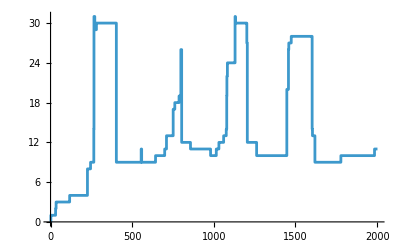

```mathematica
ListStepPlot[evo[[All, -1]]]
```

### Host parasite perturbation battle

#### Less aggressive

```mathematica
therapyevo = 
Module[{ i = 5, ltgoal ,  pca,llt, ca, initpert = <|{23,111}->2|>, initca, initlt, initaps,
plt, ru = {299459058088077823758143088095350287424,4,1}},
SeedRandom[333557 + i];
initca = {{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {200, {-110, 110}}, initpert];
initlt = Replace[{{"[◼]", "TestCALifeTime"}}[initca], -Infinity:> 401];
initaps = Select[{{"[◼]", "allperts"}}[First[initca], ru[[2]]], Keys[#][[1, 1]]>= Keys[initpert][[-1, 1]]&];
ltgoal = normlt =  {{"[◼]", "TestCALifeTime"}}[ CellularAutomaton[ru, {{1}, 0}, {200, {-110, 110}}]];
j = 0;
Reap[Sow[{initpert, initlt, initlt}];
NestWhile[
Function[{fitness, perts, aps},
pca = {{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {400, {-110, 110}}, Join[perts, RandomChoice[aps]]];
llt={{"[◼]", "TestCALifeTime"}}[First[pca]];plt = Replace[llt, -Infinity:> 401];
ltgoal = If[EvenQ[j], normlt, initlt];
Sow[{Last[pca],llt,If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal],plt,fitness]}];
If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal], j = j +1;{plt, Join[perts, Last[pca]],Select[{{"[◼]", "allperts"}}[First[pca], ru[[2]]], Keys[#][[1, 1]]>= Keys[Last[pca]][[-1, 1]]&]}, {fitness, perts, aps}]
]@@#&, {initlt,initpert, initaps},Last[#]=!={}&,1,14]][[2, 1]]];
```

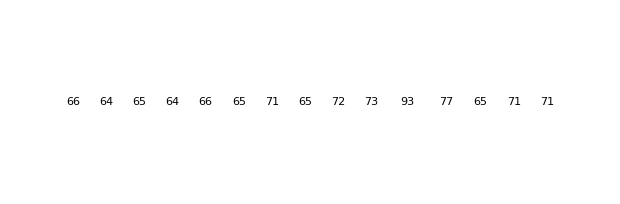

```mathematica
GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}}, #[[1]]],FrameStyle->If[#[[2]]==#[[3]],Directive[Black,Thick],Automatic],ImageSize->{Automatic,180}],Text[Style[#[[2]],Small]]]&/@therapyevo]
```

#### More aggressive

Odd number trying to stay at the sick state, even number trying to get back to the healthy state

```mathematica
txiseq[i_,cut_,max_]:=Module[{plt,ilt,iaps,ru={299459058088077823758143088095350287424,4,1},ip=<|{23,111}->2|>,ica},ica = {{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {200, {-110, 110}}, ip];ilt = Replace[{{"[◼]", "TestCALifeTime"}}[ica], -Infinity:> 401];
iaps = Select[{{"[◼]", "allperts"}}[First[ica], ru[[2]]], Keys[#][[1,1]]-Keys[ip][[-1,1]]==cut&];
ltgoal = normlt =  {{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru, {{1}, 0}, {200, {-110, 110}}]];With[{ttt=
Module[{ ltgoal ={{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru, {{1}, 0}, 400]], pca,llt},
SeedRandom[333557 + i];
j = 0;
Reap[Sow[{ip}];NestWhileList[
Function[{fitness, perts, aps},
pca = {{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {400, {-110, 110}}, Join[perts, RandomChoice[aps]]];
llt={{"[◼]", "TestCALifeTime"}}[First[pca]];plt = Replace[llt, -Infinity:> 401];
ltgoal = If[EvenQ[j], normlt, ilt];
Sow[{Last[pca],llt,If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal],plt,fitness]}];
If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal], j = j + 1;{plt, Join[perts, Last[pca]],Select[{{"[◼]", "allperts"}}[First[pca], ru[[2]]],Keys[#][[1,1]]-Keys[Last[pca]][[-1,1]]==cut&]}, {fitness, perts, aps}]
]@@#&, {ilt,ip, iaps},Last[#]=!={}&,1,max]]]},With[{u=Cases[ttt[[2,1]],{_,x_,x_}]},First/@Split[Take[u,If[!IntegerQ[#],Length[u],First@#]&[FirstPosition[Last/@u,101]]]]]]]
```

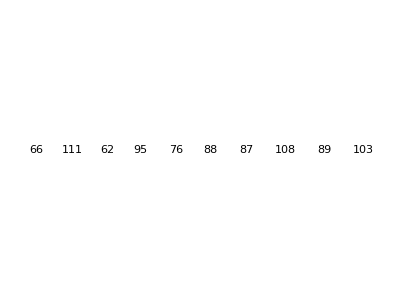

```mathematica
GraphicsGrid[Partition[Labeled[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}}, #[[1]]],ImageSize->{Automatic,180}],Text[Style[#[[2]],Small]]]&/@Prepend[txiseq[10,1,20],{<|{23,111}->2|>,66,66}],10],Spacings->12]
```